# Int 1: Governing Equations

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

$Failed

## Wheeled segway

```mathematica
With[{context="p3`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Step 2: Parameters

```mathematica
params=<| m1->1,m2->2, g->9.8 ,radius->2,i->4|>
```

<|m1→1,m2→2,g→9.8,0.385595→2,i→4|>

### Step 3: Define forces

```mathematica
xhat=RotationMatrix[θ[t]].(θhat)
yhat=RotationMatrix[Pi/2].xhat
```

{{Cos[θ[t]],-Sin[θ[t]]},{Sin[θ[t]],Cos[θ[t]]}}.θhat

{{-Sin[θ[t]],-Cos[θ[t]]},{Cos[θ[t]],-Sin[θ[t]]}}.θhat

```mathematica
fg1 =m1 g yhat;
fg2 =m2 g yhat;
fn2=normal2[t] rhat;
fdrive=drive[t] θhat;
fn1=normal[t]yhat;
ffriction = friction[t] xhat;
```

### Step 4: Equations of motion

```mathematica
(* Mass motion *)
eq1=-fg2+fn2-fdrive==m1 (polaraccel[]+x''[t] xhat);
(* Ball motion *)
eq2=-fn2+ffriction+fn1-fg1+fdrive==m2 x''[t] xhat;
(* Ball rotation *)
eq3=radius*drive[t]-radius*friction[t]==i x''[t] / radius;
eq3=FullSimplify[eq3,Assumptions->{θ[t]∈Reals}];
Column[eqns=splitVectorEqn/@{eq1,eq2,eq3}]//TraditionalForm
```

{g m2 cos(θ(t))+normal2(t)==m1 (r''(t)-r(t) (θ'(t))^2-sin(θ(t)) x''(t)),g m2 sin(θ(t))-drive(t)==m1 (2 r'(t) θ'(t)+r(t) θ''(t)+cos(θ(t)) x''(t))}
{-friction(t) sin(θ(t))+g m1 cos(θ(t))-normal(t) cos(θ(t))-normal2(t)==-m2 sin(θ(t)) x''(t),drive(t)+friction(t) cos(θ(t))+g m1 sin(θ(t))-normal(t) sin(θ(t))==m2 cos(θ(t)) x''(t)}
radius drive(t)==radius friction(t)+(i x''(t))/radius

```mathematica
(* Constraints *)
```

```mathematica
constraint=r[t]==radius;
```

```mathematica
(* Driving functions *)
```

```mathematica
driver={drive[t]==0};
```

```mathematica
(* Initial Conditions *)
initial={x[0]==0,x'[0]==0,θ[0]==.1,θ'[0]==0};
```

### Step 5: Solve

```mathematica
sol=NDSolveValue[{eqns,constraint,driver,initial}/.params,{θ[t],x[t]},{t,0,10},Method->{"IndexReduction"->{"Pantelides", "ConstraintMethod"->"Projection"}}]
```

{InterpolatingFunction[{{0., 10.}}, <>][t],InterpolatingFunction[{{0., 10.}}, <>][t]}

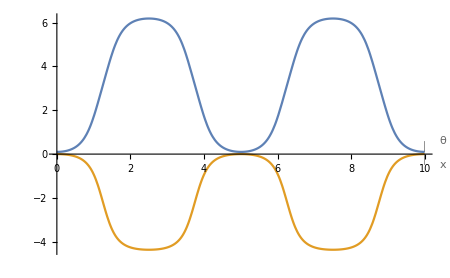

```mathematica
Plot[Evaluate@sol,{t,0,10},PlotLabels->{θ,x}]
```

### Cleanup

```mathematica
With[{context="p3`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
exportNotebookPDF[]
```

/home/eric/Documents/School/QEA2/Module 3/Int 1/Mathematica work.pdf

### Step 5: Constraints

```mathematica
constraint = r[t]==1
```

r[t]==1

```mathematica
Module[{r=r},
r[t_]:=l;
Simplify[eqns]
]
```

{g m Cos[θ]==motor[t]+l m θ'[t]^2,normal[t]==m (g Sin[θ]+l θ''[t])}

```mathematica
FullSimplify[√(Abs[Cos[θ[t]] friction[t]]^2+Abs[friction[t] Sin[θ[t]]]^2),Assumptions->{θ[t]∈Reals}]
```

Abs[friction[t]]